```mathematica
1/(1+exp(-z))
```

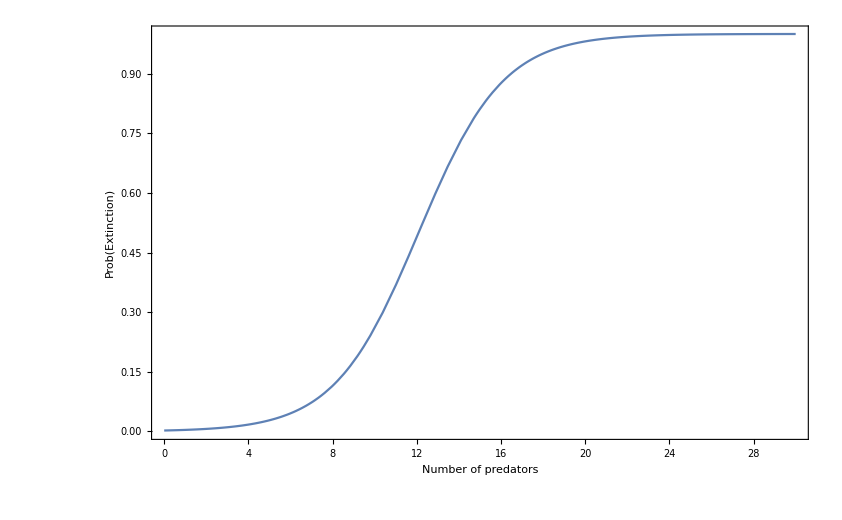

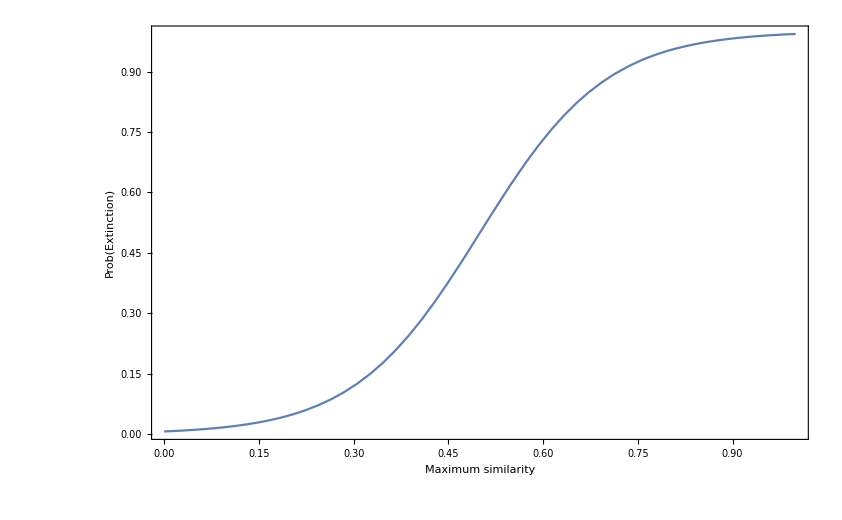

```mathematica
PredCurve = 1/(1+Exp[-0.5(x-2(L/S))]);
CompCurve = 1/(1+Exp[-10*(y-0.5)]);
Plot[PredCurve/.{L->2000,S->331},{x,0,30},PlotRange->{0,1},Frame->True,FrameLabel->{"Number of predators","Prob(Extinction)"}]
Plot[CompCurve,{y,0,1},PlotRange->All,Frame->True,FrameLabel->{"Maximum similarity","Prob(Extinction)"}]
```

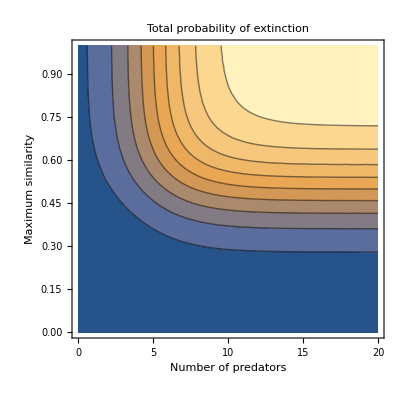

```mathematica
ContourPlot[PredCurve*CompCurve/.{L->1500,S->300},{x,0,20},{y,0,1},PlotRange->All,FrameLabel->{"Number of predators","Maximum similarity"},PlotLabel->"Total probability of extinction"]
```

```mathematica
N[2889/400]
```

7.2225

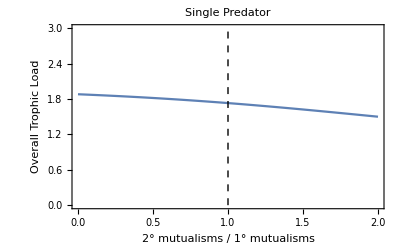

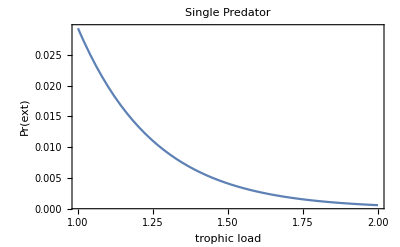

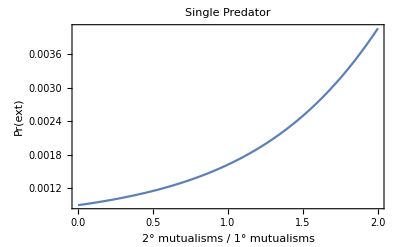

```mathematica
trophicloadsp = mintl + 1/(1/(maxtl-mintl)+mutsens*Exp[mutload-maxtl]);
prext = 1/(1+Exp[-0.5*(numpred-(trophicloadsp*Avgk))]);
prextsimple = 1/(1+Exp[-0.5*(numpred-(TL*Avgk))]);

(*Trophic Load is sigmoidal between the minimum allowed and the maximum allowed*)
Show[{
Plot[trophicloadsp/.{maxtl->2,mintl->1,mutsens->1,Avgk->8},{mutload,0,2},Frame->True,FrameLabel->{"2° mutualisms / 1° mutualisms","Overall Trophic Load"},PlotRange->All,PlotLabel->"Single Predator"],
Graphics[{Dashed,Line[{{1,0},{1,3}}]}]
}]
Show[{
Plot[prextsimple/.{Avgk->8,numpred->1},{TL,1,2},Frame->True,FrameLabel->{"trophic load","Pr(ext)"},PlotRange->All,PlotLabel->"Single Predator"](*,
Graphics[{Dashed,Line[{{1,-1},{1,0.2}}]}],
Graphics[{Dashed,Line[{{2,-1},{2,0.2}}]}]*)
}]
Show[{
Plot[prext/.{maxtl->2,mintl->1,maxtl->2,mutsens->1,numpred->1,Avgk->8},{mutload,0,2},Frame->True,FrameLabel->{"2° mutualisms / 1° mutualisms","Pr(ext)"},PlotLabel->"Single Predator"]
}]
```

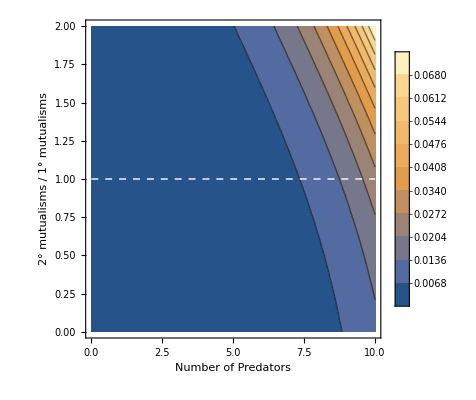

```mathematica
PrExtFig=Show[{
ContourPlot[prext/.{maxtl->2,mintl->1,mutsens->1,Avgk->10},{numpred,0,10},{mutload,0,2},FrameLabel->{Style["Number of Predators",FontSize->14],Style["2° mutualisms / 1° mutualisms",FontSize->14]},PlotRange->All,PlotLegends->Automatic,Contours->10],
Graphics[{Dashed,White,Line[{{0,1},{10,1}}]}]
}]
```

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2014_Lego/manuscript/fig_extcontour.pdf",PrExtFig]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_Lego/manuscript/fig_extcontour.pdf

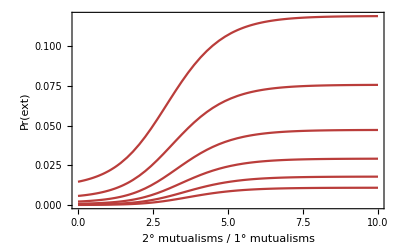

```mathematica
Show[{
Table[Plot[prext/.{maxtl->2,mintl->1,maxtl->2,mutsens->1,numpred->1,Avgk->K},{mutload,0,10},Frame->True,FrameLabel->{"2° mutualisms / 1° mutualisms","Pr(ext)"},PlotRange->All,PlotStyle->ColorData["DarkRainbow"]],
{K,5,10,1}]
}]
```

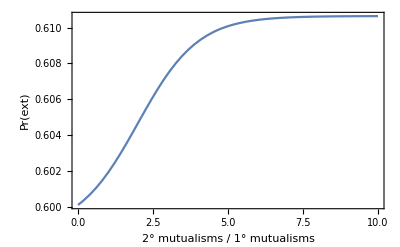
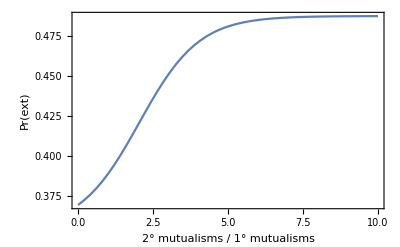
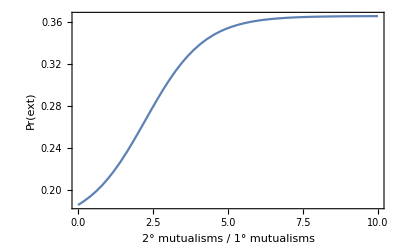
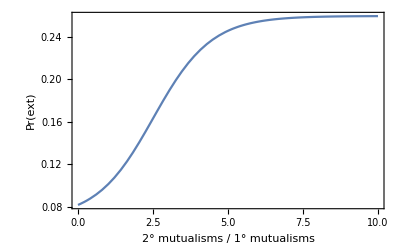
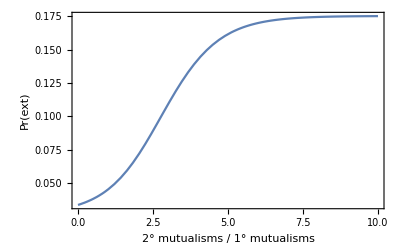
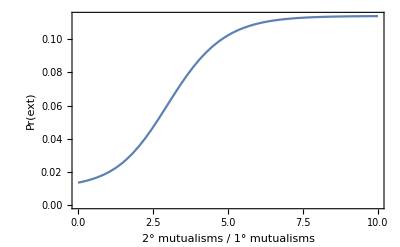
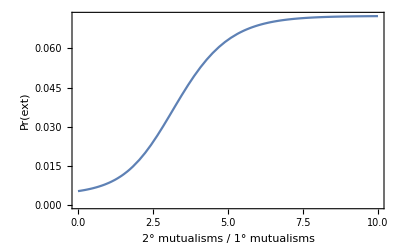
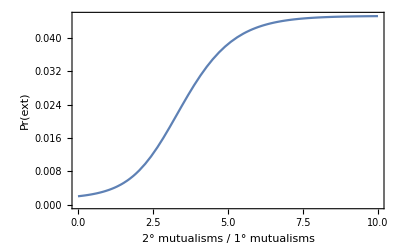

```mathematica
Table[Plot[prext/.{maxtl->2,mintl->1,maxtl->2,mutsens->1,numpred->1,Avgk->K},{mutload,0,10},Frame->True,FrameLabel->{"2° mutualisms / 1° mutualisms","Pr(ext)"}],
{K,0.1,10,1}]
```